```mathematica
(***  Mathematica modules for the (exact) pdf's (probability density functions) and cdf's (cumulative distribution functions) of the l.r.t. (likelihood ratio test) statistics Lambda_1 (L1), Lambda_2 (L2) and Lambda_3 (L3) in Section 2, and their negative logarithms    ***)

(***  Also modules are provided for the (exact) c.f.'s (characteristic functions) of the negative logarithms of all three LRT statistics, mainly because from these it is very easy to obtain the values for the moments of the corresponding LRT statistics, by computing these on -1*I, -2*I, ..., in order to obtain the first, second, ..., non-central moments of the LRT statistic     ***)


$MaxExtraPrecision=500;

(*  Base Module for the computation of the coefficients c_{j,k} in the pdf and cdf of the GIG (Generalized Integer Gamma) and the GNIG (Generalized Near-Integer Gamma) distributions   *)

Makec[r_,l_,p_]:=Module[{c},
c=Table[Table[1,{j,1,Max[r]}],{i,1,p}];
Table[c=ReplacePart[c,(Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,1,i-1}]*Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,i+1,p}])/(r[[i]]-1)!,{i,r[[i]]}],{i,1,p}];
Table[Table[c=ReplacePart[c,Sum[((r[[i]]-k+j-1)!*(Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,1,i-1}]+Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,i+1,p}])*c[[i]][[r[[i]]-(k-j)]])/(r[[i]]-k-1)!,{j,1,k}]/k,{i,r[[i]]-k}],{k,1,r[[i]]-1}],{i,1,p}];
c
]

(*  Module for the pdf of the GIG (Generalized Integer Gamma distribution  *)

GIGpdf[r_,li_,z_]:=Module[{p,l},If[Count[r,_Integer]==Length[r]&&And@@Positive[r]&&And@@Positive[li]&&Length[r]==Length[li],
p=Length[r];
l=Rationalize[li,0];
c=Makec[r,l,p];
Product[l[[j]]^r[[j]],{j,1,p}]*Sum[Exp[-l[[j]]*z]*Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}],{j,1,p}]
]
]

(*  Module for the cdf of the GIG (Generalized Integer Gamma distribution  *)

GIGcdf[r_,li_,z_]:=Module[{p,l,c},If[Count[r,_Integer]==Length[r]&&And@@Positive[r]&&And@@Positive[li]&&Length[r]==Length[li],
p=Length[r];
l=Rationalize[li,0];
c=Makec[r,l,p];
1-Product[l[[j]]^r[[j]],{j,1,p}]*Sum[Exp[-l[[j]]*z]*Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}],{j,1,p}]
]
]

(*** Modules for the c.f. (characteristic function), pdf and cdf of W1=-Log(Lambda_1) and for the pdf and cdf of Lambda_1 (L1)  ***)

(***  The arguments for these modules are (in this order): i) a vector whose components are the number of variables in each group, ii) the sample size, iii) the running variable for the function   ***)

CFW1[pk_,n_,t_]:=Product[Product[Gamma[n-j]*Gamma[n-Total[Drop[pk,k]]-j-n*I*t]/(Gamma[n-Total[Drop[pk,k]]-j]*Gamma[n-j-n*I*t]),{j,1,pk[[k]]}],{k,1,Length[pk]-1}]

PDFW1[pk_,n_,z_]:=Module[{p,hj,rj},
p=Total[pk];
hj=Table[Count[pk-(j-1),_?Positive],{j,1,p-1}]-1;
rj=Table[0,{j,1,p-1}];
rj[[1]]=hj[[1]];
Do[rj[[j]]=rj[[j-1]]+hj[[j]],{j,2,p-1}];
GIGpdf[rj,Table[(n-1-j)/n,{j,1,p-1}],z]
]

CDFW1[pk_,n_,z_]:=Module[{p,hj,rj},
p=Total[pk];
hj=Table[Count[pk-(j-1),_?Positive],{j,1,p-1}]-1;
rj=Table[0,{j,1,p-1}];
rj[[1]]=hj[[1]];
Do[rj[[j]]=rj[[j-1]]+hj[[j]],{j,2,p-1}];
GIGcdf[rj,Table[(n-1-j)/n,{j,1,p-1}],z]
]

PDFL1[pk_,n_,z_]:=PDFW1[pk,n,-Log[z]]*1/z

CDFL1[pk_,n_,z_]:=1-CDFW1[pk,n,-Log[z]]




(*** Modules for the c.f. (characteristic function), pdf and cdf of W2 and for the pdf and cdf of Lambda_2 (L2)  ***)

(***  The arguments for these modules are (in this order): i) the number of variables (p), ii) the number of mean vectors (q), iii) the sample size (n), iv) the running variable for the function   ***)

CFW2[p_,q_,n_,t_]:=Product[Gamma[n-1-j]*Gamma[n-q-j-n*I*t]/(Gamma[n-q-j]*Gamma[n-1-j-n*I*t]),{j,0,p-1}]

PDFW2[p_,q_,n_,z_]:=Module[{},
hj=Table[Count[{p,q-1}-(j-1),_?Positive],{j,1,p+q-2}]-1;
rj=Table[0,{j,1,p+q-2}];
rj[[1]]=hj[[1]];
Do[rj[[j]]=rj[[j-1]]+hj[[j]],{j,2,p+q-2}];
GIGpdf[rj,Table[(n-1-j)/n,{j,1,p+q-2}],z]
]

CDFW2[p_,q_,n_,z_]:=Module[{},
hj=Table[Count[{p,q-1}-(j-1),_?Positive],{j,1,p+q-2}]-1;
rj=Table[0,{j,1,p+q-2}];
rj[[1]]=hj[[1]];
Do[rj[[j]]=rj[[j-1]]+hj[[j]],{j,2,p+q-2}];
GIGcdf[rj,Table[(n-1-j)/n,{j,1,p+q-2}],z]
]

PDFL2[p_,q_,n_,z_]:=PDFW2[p,q,n,-Log[z]]*1/z

CDFL2[p_,q_,n_,z_]:=1-CDFW2[p,q,n,-Log[z]]


(*** Modules for the c.f. (characteristic function), pdf and cdf of W3 and for the pdf and cdf of Lambda_3 (L3)  ***)

(***  The arguments for these modules are (in this order): i) the number of variables (or rows in the matrix of mean values)(p), ii) the number of columns in the matrix of mean values (q), iii) the sample size (n), iv) the running variable for the function   ***)

CFW3[p_,q_,n_,t_]:=Product[Gamma[n+1-j]*Gamma[n+1-q-j-n*I*t]/(Gamma[n+1-q-j]*Gamma[n+1-j-n*I*t]),{j,1,p}]

PDFW3[p_,q_,n_,z_]:=Module[{},
hj=Table[Count[{p,q}-(j-1),_?Positive],{j,1,p+q-1}]-1;
rj=Table[0,{j,1,p+q-1}];
rj[[1]]=hj[[1]];
Do[rj[[j]]=rj[[j-1]]+hj[[j]],{j,2,p+q-1}];
GIGpdf[rj,Table[(n-j)/n,{j,1,p+q-1}],z]
]

CDFW3[p_,q_,n_,z_]:=Module[{},
hj=Table[Count[{p,q}-(j-1),_?Positive],{j,1,p+q-1}]-1;
rj=Table[0,{j,1,p+q-1}];
rj[[1]]=hj[[1]];
Do[rj[[j]]=rj[[j-1]]+hj[[j]],{j,2,p+q-1}];
GIGcdf[rj,Table[(n-j)/n,{j,1,p+q-1}],z]
]

PDFL3[p_,q_,n_,z_]:=PDFW3[p,q,n,-Log[z]]*1/z

CDFL2[p_,q_,n_,z_]:=1-CDFW2[p,q,n,-Log[z]]
```

```mathematica
(*****   Examples of use which work also as 'verifications'   *****)
```

```mathematica
(*   For Lambda_1  and  W1  *)
```

```mathematica
(* The 3rd moment of W1 computed from its c.f. *)
```

```mathematica
pk={5,3,4};
n=15;
SetPrecision[I^(-3)*D[CFW1[pk,n,t],{t,3}]/.t->0,30]
```

813543.903923086369791762301

```mathematica
NIntegrate[w^3*PDFW1[pk,n,w],{w,0,10^5},MaxRecursion->20,WorkingPrecision->27]
```

813543.903923086369791762301

```mathematica
(*  On the relation between the pdf and the cdf of W1   *)
```

```mathematica
NIntegrate[PDFW1[pk,n,z],{z,0,1236/10},WorkingPrecision->70]
```

0.9808561421027277457676060539860533859004379638986943912858380213146628

```mathematica
SetPrecision[CDFW1[pk,n,1236/10],75]
```

0.9808561421027277457676060539860533859004379638986943912858380213146628

```mathematica
(*  The second moment of Lambda_1  *)
```

```mathematica
SetPrecision[NIntegrate[PDFL1[pk,n,z]*z^2,{z,0,1},MaxRecursion->16,WorkingPrecision->100],35]
```

2.8863316264850643503804245468613792×10^-32

```mathematica
SetPrecision[CFW1[pk,n,2*I],35]
```

2.8863316264850643503804245468613792×10^-32

```mathematica
(*  On the relation between the pdf and cdf of Lambda_1   *)
```

```mathematica
SetPrecision[PDFL1[pk,n,1/1000],155]
SetPrecision[D[CDFL1[pk,n,z],z]/.z->1/1000,155]
```

7.557110311152407542206191076526204050348747245811165582300791450759856465833555215990155141×10^-31

7.557110311152407542206191076526204050348747245811165582300791450759856465833555215990155141×10^-31

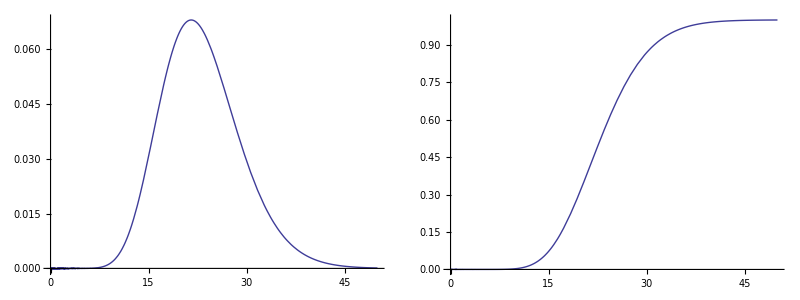

```mathematica
Grid[{{Plot[PDFW2[p,q,n,z],{z,0,50}],Plot[CDFW2[p,q,n,z],{z,0,50}]}}]
```

```mathematica
(*   For Lambda_2  and  W2  *)
```

```mathematica
(* The 3rd moment of W2  *)
```

```mathematica
p=5;
q=4;
n=15;
SetPrecision[I^(-3)*D[CFW2[p,q,n,t],{t,3}]/.t->0,38]
N[NIntegrate[PDFW2[p,q,n,z]*z^3,{z,0,Infinity},WorkingPrecision->38],35]
```

15057.19080823173962489691715510851

15057.190808231739624896917155108514

```mathematica
(*  On the relation between the p.d.f. and the c.d.f. of W2   *)
```

```mathematica
SetPrecision[NIntegrate[PDFW2[p,q,n,z],{z,0,123/10},WorkingPrecision->65],58]
```

0.01779590725895200655920795844124982995093586554843966622452

```mathematica
SetPrecision[CDFW2[p,q,n,123/10],70]
```

0.01779590725895200655920795844124982995093586554843966622452

```mathematica
(*  The second moment of Lambda_2  *)
```

```mathematica
NIntegrate[PDFL2[p,q,n,z]*z^2,{z,0,1},MaxRecursion->16,WorkingPrecision->75]
```

7.67411182444847878864738825157831198854924586856387147837590110520361541868×10^-10

```mathematica
SetPrecision[CFW2[p,q,n,2*I],75]
```

7.67411182444847878864738825157831198854924586856387147837590110520361541868×10^-10

```mathematica
(*  On the relation between the p.d.f. and c.d.f. of Lambda_2   *)
```

```mathematica
SetPrecision[PDFL2[p,q,n,1/1000],155]
SetPrecision[D[CDFL2[p,q,n,z],z]/.z->1/1000,155]
```

0.12220964786432421994017933680616901000740805823185482587288121163540142241868895142853049311584444719401026286460686329708244523641157496242

0.12220964786432421994017933680616901000740805823185482587288121163540142241868895142853049311584444719401026286460686329708244523641157496242

```mathematica
(*  Plots of the pdf and cdf of W2   *)
```

```mathematica
Grid[{{Plot[PDFW2[p,q,n,z],{z,0,50}],Plot[CDFW2[p,q,n,z],{z,0,50}]}}]
```

-Graphics-

```mathematica
(*   For Lambda_3  and  W3  *)
```

```mathematica
(* The 3rd moment of W3  *)
```

```mathematica
p=6;
q=7;
n=25;
SetPrecision[I^(-3)*D[CFW3[p,q,n,t],{t,3}]/.t->0,35]
NIntegrate[PDFW3[p,q,n,z]*z^3,{z,0,10^5},MaxRecursion->20,WorkingPrecision->31]
```

209181.259048874148566196558799

209181.259048874148566196558799

```mathematica
(*  On the relation between the p.d.f. and the c.d.f. of W3   *)
```

```mathematica
NIntegrate[PDFW3[p,q,n,z],{z,0,359/10},WorkingPrecision->90]
```

0.00256817254926496169992412812505981108940112730993134064172129111083834517758839673066503039

```mathematica
SetPrecision[CDFW3[p,q,n,359/10],100]
```

0.0025681725492649616999241281250598110894011273099313406417212911108

```mathematica
(*  The second moment of Lambda_3  *)
```

```mathematica
N[NIntegrate[PDFL3[p,q,n,z]*z^2,{z,0,1},MaxRecursion->20,WorkingPrecision->90],25]
```

8.846665779477497192711095×10^-25

```mathematica
SetPrecision[CFW3[p,q,n,2*I],25]
```

8.846665779477497192711095×10^-25

```mathematica
(*  On the relation between the p.d.f. and c.d.f. of Lambda_3   *)
```

```mathematica
SetPrecision[PDFL3[p,q,n,1/10000],155]
SetPrecision[D[CDFL3[p,q,n,z],z]/.z->1/10000,155]
```

2.3683794326199277796436470764616343953578527388950109981603868206694109338149044954090311424908×10^-15

2.3683794326199277796436470764616343953578527388950109981603868206694109338149044954090311424908×10^-15

```mathematica
(*  Plots of the pdf and cdf of W3   *)
```

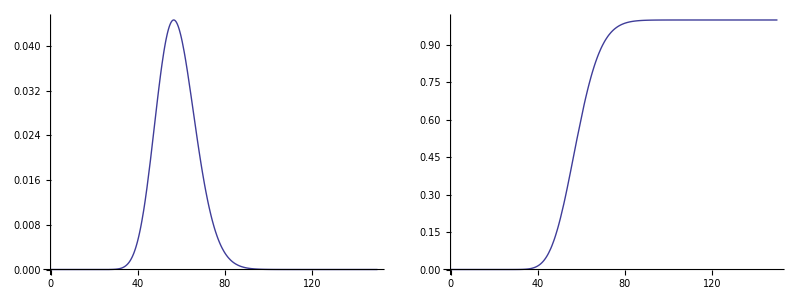

```mathematica
p=6;
q=7;
n=25;
Grid[{{Plot[SetPrecision[PDFW3[p,q,n,Rationalize[z,0]],40],{z,0,150}],Plot[SetPrecision[CDFW3[p,q,n,Rationalize[z,0]],40],{z,0,150}]}}]
```